## Definitions

```mathematica
$Assumptions=ϕ>0;
```

```mathematica
allConfigurations=Flatten[#,5]&@Table[{a,b,c,i1,i2,i3},{a,0,1},{b,0,1},{c,0,1},{i1,0,1},{i2,0,1},{i3,0,1}];

allowedConfigurations=Cases[allConfigurations,{a_,b_,c_,i1_,i2_,i3_}/;i1+i2+i3!=1&&a+c+i3!=1&&a+b+i1!=1&&b+c+i2!=1];

badConfigurations= Complement[allConfigurations,allowedConfigurations];
```

```mathematica
(* Fusion rules *)
fusion[0,0]={0};
fusion[0,1]={1};
fusion[1,0]={1};
fusion[1,1]={0,1};

δ[a_,b_,c_]:=0;
δ[0,0,0]=1;
δ[1,0,1]=1;
δ[0,1,1]=1;
δ[1,1,0]=1;
δ[1,1,1]=1;

Nn[a_,b_][c_]:=δ[a,b,c]

(* Check whether a×b = c + ... is valid fusion channel *)
legalFusionQ[a_,b_,c_]:=MemberQ[fusion[a,b],c];

(* Checks valid fusions in F-symbol *)
allowedFQ[a_,b_,c_,d_,e_,f_]:=legalFusionQ[a,b,c]&&legalFusionQ[c,d,e]&&legalFusionQ[b,d,f]&&legalFusionQ[a,f,e];
```

```mathematica
(* Quantum Dimensions *)
d[0]=1;
d[1]=ϕ;
```

```mathematica
(* --- F-symbols: Subscript[(F^abc), def] --- *)
(* Illegal channels = 0 *)
F[a_,b_,c_][d_,e_,f_]/;!allowedFQ[a,b,c,d,e,f]:=0;
(* Legal channels defaulted to 1 *)F[a_,b_,c_][d_,e_,f_]/;allowedFQ[a,b,c,d,e,f]:=1;

(*F[a_,b_,c_][d_,e_,f_]:=1;*)
F[1,1,0][1,1,0]=1/ϕ;
F[1,1,0][1,1,1]=1/Sqrt[ϕ];
F[1,1,1][1,1,0]=1/Sqrt[ϕ];
F[1,1,1][1,1,1]=-1/ϕ;
coeff[{a_,b_,c_, i1_, i2_, i3_}]:=F[c,a,i3][i1,i2,b]F[c,b,i2][b,c,0]F[b,a,i1][a,b,0]d[a]d[b]d[c]
```

```mathematica
G[i_,j_,m_][k_,l_,n_]:=1/Sqrt[d[m]d[n]] F[i,j,m][k,l,n]
```

```mathematica
(* Illegal channels = 0 *)
R[c_][a_,b_]/;!legalFusionQ[a,b,c]:=0;
(* Legal channels defaulted to 1 *)
R[c_][a_,b_]/;legalFusionQ[a,b,c]:=1;

R[0][1,1]=Exp[-4π I/5];
R[1][1,1]=Exp[3π I/5];
```

```mathematica
(* F-Symbols: Choi et al convention Subscript[(Subscript[F, abc]^d), (e)(f)] *)
```

```mathematica
FF[a_,b_,c_][d_]:=Table[
F[a,b,x][c,d,y],{y,0,1},{x,0,1}
]

FFinv[a_,b_,c_][d_]:=Table[
F[a,b,x][c,d,y],{x,0,1},{y,0,1}
]
```

```mathematica
(* Graphics *)
(*RP = RegularPolygon[6];*)
lineThickness=0.03;

δ[1]={0,0};
δ[2]={3/2,-Sqrt[3]/2};
δ[3]={3/2,Sqrt[3]/2};

P[1]={1/2,-(√3)/2};
P[2]=RotationMatrix[2π/3]. (P[1]-{1,0}) + {1,0};
P[3]=RotationMatrix[2 2π/3]. (P[1]-{1,0}) + {1,0};



(* i'th and j'th edge is removed *)
hex[i_,j_]:=Module[{pts,edges,pairs,lines},
pts=CirclePoints[6];
edges=Partition[Append[pts,First@pts],2,1];

pairs = Table[{x,Mod[x+1,6,1]},{x,1,6}];

pairs = Delete[pairs,{{i},{j}}];

lines={Red,CapForm["Round"],Thickness[lineThickness],Line[
{pts[[#[[1]]]],pts[[#[[2]]]]}&/@pairs
]};

lines
]

hexagon[{x_,y_},i_]:=Translate[{ hex[x,y]},δ[i]]

bg=Translate[{Blue,RegularPolygon[6]},δ[#]]&/@{1,2,3};

line[line_]:={Red,CapForm["Round"],Thickness[lineThickness],Line[{P[line],{1,0}}]};

spin[σ_,shape_]:=If[σ==0,{},shape]
```

```mathematica
Configuration[{a_,b_,c_, i1_, i2_, i3_}, imageSize_:400]:=
Graphics[{
bg,
spin[a,hexagon[{1,2},1]],
spin[b,hexagon[{3,4},2]],
spin[c,hexagon[{5,6},3]],
spin[i1,line[1]],
spin[i2,line[2]],
spin[i3,line[3]]
},
PlotRange->{{-1.1,2.6},{-1.8,1.8}}, ImageSize->imageSize
]
```

## States

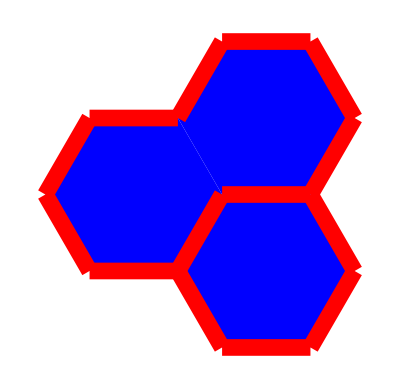

```mathematica
Configuration[{1,1,1,1,1,0}]
```

```mathematica
stringNets=Configuration[#,30]&/@allowedConfigurations;
coeffs=coeff/@allowedConfigurations;
```

```mathematica
stringNetWeights={coeffs[[#]],stringNets[[#]]}&/@Range[Length@allowedConfigurations]
```

{{1,-Graphics-},{ϕ,-Graphics-},{ϕ,-Graphics-},{ϕ,-Graphics-},{ϕ^(3/2),-Graphics-},{ϕ,-Graphics-},{ϕ,-Graphics-},{ϕ^(3/2),-Graphics-},{ϕ,-Graphics-},{ϕ^(3/2),-Graphics-},{ϕ,-Graphics-},{ϕ^(3/2),-Graphics-},{ϕ^(3/2),-Graphics-},{ϕ^(3/2),-Graphics-},{-ϕ,-Graphics-}}

```mathematica
(*Configuration[#,100]&/@badConfigurations*)
```

```mathematica
Ket[{ψ}]==1/M Plus@@(#[[1]]Ket[{#[[2]]}]&/@stringNetWeights)
```

ψ==1/M(-Graphics-+ϕ -Graphics-+ϕ -Graphics-+ϕ -Graphics-+ϕ^(3/2) -Graphics-+ϕ -Graphics-+ϕ -Graphics-+ϕ^(3/2) -Graphics-+ϕ -Graphics-+ϕ^(3/2) -Graphics-+ϕ -Graphics-+ϕ^(3/2) -Graphics-+ϕ^(3/2) -Graphics-+ϕ^(3/2) -Graphics--ϕ -Graphics-)

```mathematica
Configuration[{1,1,1,1,1,0}]
```

-Graphics-

## Tube Algebra (OLD VERSION)

### Definitions (Half-Braiding) of fusion category

For a fusion category, C, we have that Z(C) = Rep(Tube(C)).

Simple objects of the Drinfeld center Z(C) consists of pairs (Z, γ_Z) where Z is a (generally non-simple) element of C and γ is the half-braiding isomorphisms. γ has to satisfy a Hexagon equation for consistency.

If C is modular, there is an explicit way to express γ in terms of the data of C (F and R matrices). The expression given in Hu et al, does not satisfy the “neutrality equation” they state.

I have derived them myself from, following the notation of Choi et al, and they are satisfied. And give access to minimal central idempotents of Tube(C).

```mathematica
(* Hu et al convensions: Has some errors it appears *)
z[{i_,jj_}][p_,j_,q_,t_]:=KroneckerDelta[jj,j] Sum[d
[a]d[b]R[a][i,k]R[b][j,k]
G[a,i,k][b,j,t]G[i,j,q][t,k,a]G[i,b,t][k,p,j]
,{a,0,1},{b,0,1},{k,0,1}]//Simplify//Collect[#,ϕ]&

(* They call it neutrality, but I believe it's just the hexagon realtions. *)
neutralityConditionCheck[z_]:=
Flatten@Table[Sum[d[r]d[s]z[J][l,n,q,r]z[J][p,m,l,s]G[m,s,l][n,r,t]G[s,p,m][j,n,t]G[m,t,r][q,n,k],{l,0,1},{r,0,1},{s,0,1}] == δ[m,n,j] KroneckerDelta[j,k]/d[j] z[J][p,j,q,t],
{m,0,1},{n,0,1},{j,0,1},{k,0,1},{p,0,1},{q,0,1},{t,0,1},{J,Tuples[{0,1},2]}
]
```

```mathematica
(* Choi et al *)
Ω[d_][c_,μ_][e_,f_]:=Sum[
FFinv[c,μ[[1]],μ[[2]]][d][[h+1,f+1]]
R[h][c,μ[[1]]]
FF[μ[[1]],c,μ[[2]]][d][[g+1,h+1]]
Conjugate[R[g][μ[[2]],c]]
FFinv[μ[[1]],μ[[2]],c][d][[e+1,g+1]],
{g,0,1},{h,0,1}
]
```

```mathematica
halfBraidingHexagonConditionCheck[Ω_]:=
Table[
Sum[
Ω[e][a,μ][d,f]
FFinv[a,f,b][c][[e+1,g+1]]
Ω[g][b,μ][f,h]
,
{f,0,1}]
==
Sum[FFinv[d,a,b][c][[e+1,ap+1]]Ω[c][ap,μ][d,h]FFinv[a,b,h][c][[ap+1,g+1]]
,{ap,0,1}],
{a,0,1},{b,0,1},{c,0,1},{d,0,1},{g,0,1},{e,0,1},{h,0,1},{μ,Tuples[{0,1},2]}]
```

```mathematica
(* The equations *)
neutralityConditionCheck[z]//ReplaceAll[#,ϕ->(Sqrt[5]+1)/2]&//FullSimplify//Flatten//AllTrue[#,#==True&]&
```

False

```mathematica
halfBraidingHexagonConditionCheck[Ω]//ReplaceAll[#,ϕ->(Sqrt[5]+1)/2]&//FullSimplify//Flatten//AllTrue[#,#==True&]&
```

True

```mathematica
(* S-matrix for Z(C) - double Fibonacci *)
Sfib = 1/Sqrt[ϕ+2]{{1,ϕ},{ϕ,-1}};
SdoubleFib[μ_,ν_]:=Sfib[[μ[[1]]+1,ν[[1]]+1]]Sfib[[ν[[2]]+1,μ[[2]]+1]]
```

### Definitions (Tube algebra product)

```mathematica
bProd[B[p_,s_,q_,u_],B[pt_,st_,qt_,ut_]]:=KroneckerDelta[pt,q]*Sum[Sqrt[(d[s]d[st])/d[β]]F[ut,st,q][u,s,α]F[st,qt,ut][α,s,β]F[α,st,u][s,p,β]B[p,β,qt,α],{α,0,1},{β,0,1}];


(*Split an expression into additive terms*)bTerms[expr_]:=Module[{e=Expand[expr]},If[Head[e]===Plus,List@@e,{e}]];

(*For a single term,extract coefficient and basis*)
bCoeff[term_]:=term/. (c_. B[___]:>c);
bBasis[term_]:=term/. (c_. b_B:>b);

(*Multiply two superpositions by bilinearity*)
MultiplyB[x_,y_]:=Module[{tx=bTerms[x],ty=bTerms[y]},Collect[Total@Flatten@Table[bCoeff[tx[[i]]] bCoeff[ty[[j]]]*bProd[bBasis[tx[[i]]],bBasis[ty[[j]]]],{i,Length[tx]},{j,Length[ty]}],_B]];
```

```mathematica
(* Test *)
MultiplyB[ B[1,1,1,1],α B[1,1,1,1]+ β B[1,0,1,1]]//Collect[#,{α,β}]&
```

β B[1,1,1,1]+α (-B[1,0,1,1]/(√(ϕ^2))+B[1,1,1,0]-B[1,1,1,1]/ϕ^(5/2))

### Minimal central idempotents of Tube(C) algebra

```mathematica
(* To make mathematica simplify properly *)
toϕ[expr_]:=ReplaceAll[expr,Sqrt[5]->2 ϕ-1]//FullSimplify
toPhase[expr_]:=expr/. Power[-1,r_Rational]:>Exp[I Pi r]

tubeSimplify[expression_]:=expression/.ϕ->(Sqrt[5]+1)/2//Collect[#,_B]&//Plus@@FullSimplify/@List@@#&//toϕ//toPhase
```

```mathematica
(* Minimal central idempotents for a modular category C *)
(* 2+ϕ added extra for simpler normalization *)
Π[μ_]:=Block[{c,idempotent},
idempotent=Sum[Sqrt[d[dd]/(d[a]d[c])]Ω[dd][a,ν][c,c]SdoubleFib[μ,ν]SdoubleFib[μ,{0,0}]B[a,c,a,dd],
{a,0,1},{c,0,1},{dd,0,1},{ν,Tuples[{0,1},2]}];

(* Normalizations to simplify expression *)
If[μ=={1,1}, c = (2+ϕ)/ϕ^2,c=2+ϕ];

c idempotent//tubeSimplify
]
```

```mathematica
(* Simple objects of Drinfeld center (double category)*)
Zc = Tuples[{0,1},2];

(* Π[μ] for μ∈Z(C)*)
Π[#]&/@Zc//TubeRepresentation//MatrixForm
```

(ϕ -Graphics-+-Graphics-
-ⅇ^((ⅈ π)/5) -Graphics-+-Graphics-+-Graphics- 
ⅇ^((4 ⅈ π)/5) -Graphics-+-Graphics-+-Graphics- 
-(-Graphics-)/ϕ+-Graphics-+(-1+ϕ) (-Graphics-+-Graphics-)+-Graphics- )

```mathematica
Π0=B[0,0,0,0]+ϕ B[0,1,0,1];
Π1=B[1,0,1,1]-ⅇ^((ⅈ π)/5) B[1,1,1,0]+Sqrt[ϕ] ⅇ^((ⅈ 3π)/5)B[1,1,1,1];
Π2=B[1,0,1,1]+ⅇ^((4ⅈ π)/5) B[1,1,1,0]+Sqrt[ϕ] ⅇ^((-ⅈ 3π)/5)B[1,1,1,1];
Π3=B[0,0,0,0]-B[0,1,0,1]/ϕ+(ϕ-1) (B[1,0,1,1]+B[1,1,1,0])+ϕ^(-5/2)B[1,1,1,1];
```

```mathematica
(* Expressed more nicely *)
idempotents={Π0,Π1,Π2,Π3};
idempotents//TubeRepresentation//MatrixForm
```

(ϕ -Graphics-+-Graphics-
-ⅇ^((ⅈ π)/5) -Graphics-+ⅇ^((3 ⅈ π)/5) √ϕ -Graphics-+-Graphics-
ⅇ^((4 ⅈ π)/5) -Graphics-+ⅇ^(-(3 ⅈ π)/5) √ϕ -Graphics-+-Graphics-
-(-Graphics-)/ϕ+-Graphics-+(-Graphics-)/ϕ^(5/2)+(-1+ϕ) (-Graphics-+-Graphics-))

```mathematica
(* Idempotency check: Π[μ]^2=Π[μ]*)
MultiplyB[Π[#],Π[#]]==Π[#]&/@Tuples[{0,1},2].
```

{True,True,True,True}

```mathematica
(* Idempotency check: Π[μ]xΠ[ν]=Subscript[δ, μ,ν] Π[μ]*)
Table[MultiplyB[Π[μ],Π[ν]]==KroneckerDelta[μ,ν]Π[μ],{μ,Tuples[{0,1},2]},{ν,Tuples[{0,1},2]}]//ReplaceAll[#,ϕ->(Sqrt[5]+1)/2]&//FullSimplify
```

$Aborted

```mathematica
fullBasis=B@@#&/@Tuples[{0,1},4];
```

```mathematica
twistFull=MultiplyB[B[1,1,1,0],#]&/@fullBasis//FullSimplify
```

{0,0,0,0,0,0,0,0,0,0,0,B[1,1,1,0],0,B[1,1,0,1],(B[1,0,1,1]+√ϕ B[1,1,1,1])/ϕ,(√ϕ B[1,0,1,1]-B[1,1,1,1])/ϕ}

```mathematica
nonZeroPositions=Flatten@Position[twistFull,Except[0],{1},Heads->False];
```

```mathematica
partialBasis=fullBasis[[nonZeroPositions]];
partialTwist=twistFull[[nonZeroPositions]];
```

```mathematica
{const,mat}=CoefficientArrays[partialTwist,partialBasis];
```

```mathematica
θ=Normal@mat//Simplify[#,Assumptions->ϕ>0]&;
```

```mathematica
θ//MatrixForm
```

(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1/ϕ | 0 | 0 | 1/(√ϕ)
1/(√ϕ) | 0 | 0 | -1/ϕ)

```mathematica
v1={Exp[(-I 4π)/5],0,1,Sqrt[ϕ]Exp[3π I/5]} ;
v2={Exp[(I 4π)/5],0,1,Sqrt[ϕ]Exp[-3π I/5]} ;
v3={1,0,1,ϕ^(-3/2)} ;
v4 = {0,1,0,0};

eigenVecs = {v1,v2,v3,v4};
eigenVals={Exp[(I 4π)/5],Exp[(-I 4π)/5],1,1};
```

```mathematica
partialBasis
```

{B[1,0,1,1],B[1,1,0,1],B[1,1,1,0],B[1,1,1,1]}

```mathematica
θ.#[[1]]==#[[2]]#[[1]]&/@Transpose[{eigenVecs,eigenVals}]/.ϕ->(Sqrt[5]+1)/2//FullSimplify
```

{True,True,True,True}

```mathematica
partialBasis//TubeRepresentation
```

TubeRepresentation[{B[1,0,1,1],B[1,1,0,1],B[1,1,1,0],B[1,1,1,1]}]

```mathematica
Π[{0,0}]/.ϕ->(Sqrt[5]+1)/2//FullSimplify
```

B[0,0,0,0]+1/2 (1+√5) B[0,1,0,1]

## X (OLD VERSION)

```mathematica
MultiplyB[Θ,#]&/@states//ReplaceAll[#,ϕ->(Sqrt[5]+1)/2]&//FullSimplify
```

{B[1,0,1,1]+√(1/2 (1+√5)) B[1,1,1,1],1/2 (1+√5) B[1,1,1,0],√(1/2 (1+√5)) B[1,0,1,1]-B[1,1,1,1]}

### Definitions (Graphics)

```mathematica
PlotTubeState[{p_,s_,q_,u_},imageSize_:400 ]:=Block[{L1,L2,L3,C1,annulus},
L1={Red,CapForm["Round"],Thickness[lineThickness],Line[{{0,0},{1,0}}]};
L2={Red,CapForm["Round"],Thickness[lineThickness],Line[{{1,0},{2,0}}]};
L3 = {Red,CapForm["Round"],Thickness[lineThickness],Line[{{2,0},{3,0}}]};
C1 = ParametricPlot[{(-2 +  t/(2π))Cos[t]+3,(-2 + t/(2π)) Sin[t]},{t,0,2π},PlotStyle->{Red,Thickness[lineThickness],CapForm["Round"]},Axes->False,Frame->False,PlotRange->All];
annulus = {{Blue,Opacity[0.8],Disk[{2.5,0},2.5]}, {Black,Disk[{3.5,0},0.5]}};

Graphics[{annulus,
spin[p,L1],spin[s,First@Normal@C1],spin[u,L2],spin[q,L3]},PlotRange->{{0,5},{-2.6,2.6}},
ImageSize->imageSize]
]
```

```mathematica
PlotTubeState3D[{p_,s_,q_,u_},imageSize_:40 ]:=Block[{L1,L2,L3,C1,cylinder,radius},
radius = 0.3;

L1={Red,CapForm["Round"],Thickness[lineThickness],Line[{{0,-radius,0},{0,-radius,1/3}}]};
L2={Red,CapForm["Round"],Thickness[lineThickness],Line[{{0,-radius,1/3},{0,-radius,2/3}}]};
L3 = {Red,CapForm["Round"],Thickness[lineThickness],Line[{{0,-radius,2/3},{0,-radius,3/3}}]};

C1 = ParametricPlot3D[{radius Cos[t+(3π)/2],radius Sin[t+(3π)/2],1/3 + t/(2π)1/3},{t,0,2π},PlotStyle->{Red,Thickness[lineThickness],CapForm["Round"]},Axes->False,PlotRange->All];

cylinder = {Opacity[.4],EdgeForm[Opacity[.4]],Cylinder[{{0,0,0},{0,0,1}},radius]};

Graphics3D[{cylinder,spin[p,L1],spin[s,First@Normal@C1],spin[u,L2],spin[q,L3]}, Boxed->False,ImageSize->imageSize]
]
```

```mathematica
TubeRepresentation[terms_]:=terms/.B[x__]:>Interpretation[Deploy@PlotTubeState[List@x,50],B[x]]


TubeRepresentation3D[terms_]:=terms/.B[x__]:>Interpretation[Deploy@PlotTubeState3D[List@x,50],B[x]]

NormalForm[expr_]:=expr/. Interpretation[_,content_]:>content;
```

```mathematica
α B[1,0,0,0] + β B[1,1,1,1] + γ B[1,0,1,0]//TubeRepresentation3D
```

α -Graphics3D-+γ -Graphics3D-+β -Graphics3D-

```mathematica
B@@#&/@Tuples[{0,1},4]//TubeRepresentation3D
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
B@@#&/@Tuples[{0,1},4]//TubeRepresentation
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
prod[{p_,s_,q_,u_},{pt_,st_,qt_,ut_}]:= KroneckerDelta[pt,q]Sum[Sqrt[(d[s]d[st])/d[β]]F[ut,st,q][u,s,α]F[st,qt,ut][α,s,β]F[α,st,u][s,p,β]B[p,β,qt,α],{α,0,1},{β,0,1}]
```

```mathematica
TubeProduct[{p_,s_,q_,u_},{pt_,st_,qt_,ut_},print_:False]:=Block[{result},

result = prod[{p,s,q,u},{pt,st,qt,ut}]//TubeRepresentation;
If[print,Print[B[p,s,q,u]×B[pt,st,qt,ut]==result//TubeRepresentation]];


result
]
```

### Tests

```mathematica
B[1,1,1,1]//TubeRepresentation
```

-Graphics-

```mathematica
B[Sequence@@#]&/@Tuples[{0,1},4]//TubeRepresentation
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TubeProduct[{1,1,1,1},{1,1,1,1},True];
```

-Graphics-×-Graphics-==-Graphics--(-Graphics-)/ϕ^(5/2)-(-Graphics-)/(√(ϕ^2))

```mathematica
TubeProduct[{0,1,1,1},{1,1,1,1},True];
```

-Graphics-×-Graphics-==(-Graphics-)/ϕ^(3/2)

```mathematica
TubeProduct[{1,1,1,1},{0,1,1,1},True];
```

-Graphics-×-Graphics-==0

### f

```mathematica
(* Condition for projectors in Subscript[A, q]⊂A *)
eqs=Table[
Π[q,β,α]==Sum[Π[q,s,u]Π[q,st,ut] Sqrt[(d[s]d[st])/d[β]]F[ut,st, q][u,s,α]F[st,q,ut][α,s,β]F[α,st,u][s,q,β],{s,0,1},{u,0,1},{st,0,1},{ut,0,1}],
{q,0,1},{β,0,1},{α,0,1}]//Flatten;

vars =Table[Π[q,β,α],{q,0,1},{β,0,1},{α,0,1}]//Flatten;
```

```mathematica
Π[0,0,1]=0;
Π[0,1,0]=0;
Π[1,0,0]=0;
```

```mathematica
projSolutions1 = {{Π[0,0,0]->x,Π[0,1,1]->c0 √(x-x^2),Π[1,1,0]->Π[1,1,1]^2/(1-2Π[1,0,1])},{Π[0,0,0]->x2,Π[0,1,1]->√(x2-x2^2),Π[1,1,0]->Π[1,1,1]^2/(1-2Π[1,0,1]),x2->(5-√5)/10}};
```

```mathematica
projSolutions2 ={{Π[1,0,1]->0,Π[1,1,1]->0},{Π[1,0,1]->1,Π[1,1,1]->0},{Π[1,0,1]->1/(√5),Π[1,1,1]->√(-2/5+1/(√5))},{Π[1,0,1]->1-1/(√5),Π[1,1,1]->-√(-2/5+1/(√5))},{Π[1,0,1]->1/2(1+c2/(√5)),Π[1,1,1]->√((√5-1)/10) ⅇ^((c1(5-c2) ⅈ π)/10)}};
```

```mathematica
allSolutions=Map[Flatten,Tuples[{projSolutions1,projSolutions2}]/. {r1_List,r2_List}:>Join[r1,r2]];
```

```mathematica
(*DeleteCases[eqs,True]/.allSolutions//FullSimplify[#]&//MatrixForm*)
```

```mathematica
proj[q_,sol_]:=Sum[Π[q,s,u]B[q,s,q,u],{s,0,1},{u,0,1}]//.sol
```

```mathematica
(* q = 0 *)
proj[0,allSolutions]-1/(1/10 (-5+√5))/.x->1//FullSimplify//DeleteDuplicates//TubeRepresentation//MatrixForm
```

(1/2 (5+√5) -Graphics-
1/2 (1+√5) -Graphics-+-Graphics-)

```mathematica
(* q = 1 *)
proj[1,allSolutions]/(1-1/(√5))/.{c1->-1,c2->1}//FullSimplify//DeleteDuplicates//TubeRepresentation//MatrixForm
```

(0
1/4 (5+√5) -Graphics-
1/4 (1+√5) (-Graphics-+√(-2+√5) -Graphics-+-Graphics-)
-1/4 (1+√5) (-Graphics-+√(-2+√5) -Graphics-)+-Graphics-
((-1)^(1/5) (-5+√5) -Graphics-+(-1)^(3/5) √(10 (-1+√5)) -Graphics--(5+√5) -Graphics-)/(2 (-5+√5)))

```mathematica
1/(-5+√5)((-5+√5) B[1,0,1,1]+(-1)^(1/5) (-5+√5) B[1,1,1,0]+(-1)^(3/5) √(10 (-1+√5)) B[1,1,1,1])//FullSimplify//TubeRepresentation
```

(-1)^(1/5) -Graphics-+-Graphics-+-Graphics-

```mathematica
//N
```

0.393076-1.20976 ⅈ

```mathematica
(-1)^(1/5)//N
```

0.809017+0.587785 ⅈ

```mathematica
-Sqrt[(Sqrt[5]+1)/2]Exp[3π I /5]//N
```

0.393076-1.20976 ⅈ

### Twist

```mathematica
Θ = B[0,0,0,0] +ϕ B[1,1,1,0]//TubeRepresentation
```

-Graphics-+ϕ -Graphics-

```mathematica
B[1,1,1,0]//TubeRepresentation
```

-Graphics-

```mathematica
states={{1,1,1,0},{1,0,1,1},{1,1,1,1}};
```

```mathematica
B@@#&/@states//TubeRepresentation
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
TubeProduct[#,{1,1,1,0},True]&/@states;
```

-Graphics-×-Graphics-==(-Graphics-)/(√ϕ)+(-Graphics-)/(√(ϕ^2))

-Graphics-×-Graphics-==-Graphics-

-Graphics-×-Graphics-==-(-Graphics-)/ϕ+(√(ϕ^2) -Graphics-)/ϕ^(3/2)

```mathematica
images=prod[#,{1,1,1,0}]&/@states
```

{B[1,0,1,1]/(√(ϕ^2))+B[1,1,1,1]/(√ϕ),B[1,1,1,0],(√(ϕ^2) B[1,0,1,1])/ϕ^(3/2)-B[1,1,1,1]/ϕ}

```mathematica
basis=B@@#&/@states
```

{B[1,1,1,0],B[1,0,1,1],B[1,1,1,1]}

```mathematica
{const,mat}=CoefficientArrays[images,basis];
```

```mathematica
θ=Normal@mat//Simplify[#,Assumptions->ϕ>0]&;
```

```mathematica
θ//MatrixForm
```

(0 | 1/ϕ | 1/(√ϕ)
1 | 0 | 0
0 | 1/(√ϕ) | -1/ϕ)

```mathematica
v1={1,Exp[(-I 4π)/5],Sqrt[ϕ]Exp[3π I/5]} ;
v2={1,Exp[(I 4π)/5],Sqrt[ϕ]Exp[-3π I/5]} ;
v3={1,1,ϕ^(-3/2)} ;


e1 = Exp[4π I/5];
e2 = Exp[-4π I/5];
e3=1;
```

```mathematica
{θ.v1-e1 v1,
θ.v2-e2 v2,
θ.v3-e3 v3}/.ϕ->(Sqrt[5]+1)/2//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Solve[5 x^2-(4c0+1x)+1==0,x]//MatrixForm
```

(x→1/10 (1-√(-19+80 c0))
x→1/10 (1+√(-19+80 c0)))

```mathematica
Solve[ϕ^2-ϕ-1==0,ϕ]
```

{{ϕ→1/2 (1-√5)},{ϕ→1/2 (1+√5)}}

```mathematica
5 8
```

40

```mathematica
GoldenRatio//N
```

1.61803

```mathematica
B[1,0,1,1]+ϕ B[1,1,1,1]//TubeRepresentation
```

ϕ -Graphics-+-Graphics-